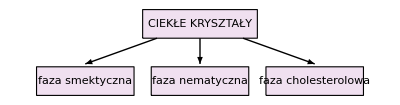

```mathematica
Show[
Graphics[{LightPurple,EdgeForm[Black],Rectangle[{4.0,4.75},{6,5.25}],
 Black, Text["CIEKŁE KRYSZTAŁY",{5,5}] }],

Graphics[{LightPurple,EdgeForm[Black],Rectangle[{4.15,3.75},{5.85,4.25}],
 Black, Text["faza nematyczna",{5,4}] }],

Graphics[{LightPurple,EdgeForm[Black],Rectangle[{2.15,3.75},{3.85,4.25}],
 Black, Text["faza smektyczna",{3,4}] }],

Graphics[{LightPurple,EdgeForm[Black],Rectangle[{6.15,3.75},{7.85,4.25}],
 Black, Text["faza cholesterolowa",{7,4}] }],

Graphics[{ Arrow[{{4.25,4.75},{ 2.15+(3.85- 2.15)/2 ,4.30}}],
Arrow[{{5.75,4.75},{ 6.15+(7.85- 6.15)/2 ,4.30}}],
Arrow[{{5,4.75},{ 5 ,4.30}}] }],

Framed -> True
]
```

```mathematica
Graphics[{Dashed,a}],
Graphics[{Red,a}],Graphics[{Thick,a}],Graphics[{Thick,Dashed,Red,a}],
```

```mathematica
(* Input geometry *)


rmax = 10;
n = 10 ;
```

```mathematica
(* Perpendicular *)

Show[ 

Graphics3D[Table[   
Table[  { Blue,Thick, Arrowheads[.02], Arrow[{{r* Cos[2k Pi/n],r*Sin[2k Pi /n], 2} ,{r*Cos[2k Pi/n],r*Sin[2k Pi /n], 5}}  ]},{k,n}], {r,0,rmax,3}  
]],

Graphics3D[Table[   
Table[  { Blue,Thick, Line[{{r* Cos[2k Pi/n],r*Sin[2k Pi /n], 5} ,{r*Cos[2k Pi/n],r*Sin[2k Pi /n], 8}}  ]},{k,n}], {r,0,rmax,3}  
]],

Graphics3D[ Table[ Table[  {Red,Thick, Arrowheads[.02], Arrow[ {{xx,-1,zz}, {xx,1,zz}} ]   }  , {zz, 4,6}] ,{xx,-2,2}]],

Graphics3D[{Opacity[0.25],Cylinder[{{0,0,0},{0,0,2}}, rmax],  Cylinder[{{0,0,8},{0,0,10}}, rmax  ] }], 

Graphics3D[
{ Opacity[0.5],  Cuboid[ {-2,-1,4}, {2,1,6}], Black,  Cuboid[ {-2.1,-1.1,3.8}, {2.1,-1,6.2}],  Cuboid[ {-2.1,1,3.8}, {2.1,1.1,6.2}] }
],
Boxed-> False,
ImageSize->Large,
AspectRatio->1,
ViewPoint->{1,0,-1}
]
```

-Graphics3D-

```mathematica
(* Parallel *)

Show[ 

Graphics3D[Table[   
Table[  { Blue,Thick, Arrowheads[.02], Arrow[{{r* Cos[2k Pi/n],r*Sin[2k Pi /n], 2} ,{r*Cos[2k Pi/n],r*Sin[2k Pi /n], 5}}  ]},{k,n}], {r,0,rmax,3}  
]],

Graphics3D[Table[   
Table[  { Blue,Thick, Line[{{r* Cos[2k Pi/n],r*Sin[2k Pi /n], 5} ,{r*Cos[2k Pi/n],r*Sin[2k Pi /n], 8}}  ]},{k,n}], {r,0,rmax,3}  
]],

Graphics3D[ Table[ Table[  {Red,Thick, Arrowheads[.02], Arrow[ {{xx,yy,4}, {xx,yy,6}} ]   }  , {yy, -1,1}] ,{xx,-2,2}]],

Graphics3D[{Opacity[0.25],Cylinder[{{0,0,0},{0,0,2}}, rmax],  Cylinder[{{0,0,8},{0,0,10}}, rmax  ] }], 

Graphics3D[
{ Opacity[0.5],  Cuboid[ {-2,-1,4}, {2,1,6}], Black,  Cuboid[ {-2.1,-1.1,3.9}, {2.1,1.1,4}],  Cuboid[ {-2.1,-1.1,6}, {2.1,1.1,6.1}] }
],
Framed-> False,
Boxed-> False,
ImageSize->Large,
AspectRatio->1,
ViewPoint-> {0,-2,2}
]
```

-Graphics3D-